```mathematica
Hint=1/Pi/b^2*Sqrt[Δ^2-b^2*Cos[px+a*Sin[x]]]
```

(√(Δ^2-b^2 Cos[px+a Sin[x]]))/(b^2 π)

```mathematica
D[f[ξ],{ξ,2}]+F[f[ξ],a]==0
```

F[ξ,a]+f''[ξ]==0

```mathematica
D[Hint,px]/.px->α
```

Sin[α+a Sin[x]]/(2 π √(Δ^2-b^2 Cos[α+a Sin[x]]))

```mathematica
F:=Compile[{{x,_Real},{a,_Real},{b,_Real}},NIntegrate[Sqrt[1+b^2*(1-Cos[x+a*Sin[t]])],{t,0.0,2*Pi},AccuracyGoal->16]]
```

```mathematica
II[alpha_,a_,b_]:=NIntegrate[1/Sqrt[F[x,a,b]-F[0,a,b]],{x,Pi,alpha}]//Quiet;
```

```mathematica
PP[a_,b_]:=Table[{II[alpha,a,b]/Sqrt[2/Pi],alpha},{alpha,10^-5,2*Pi,0.05}];
```

```mathematica
list0=PP[0,1];//Timing
```

{57.736,Null}

```mathematica
fun=Interpolation[list0,InterpolationOrder->1]
```

InterpolatingFunction[{{-13.0888,4.98175}},<>]

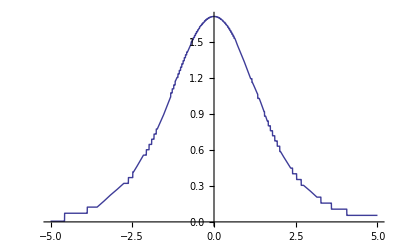

```mathematica
Plot[fun'[x],{x,-5,5}]
```

```mathematica
lp0=ListPlot[Table[{list0[[i,1]],(list0[[i+1,2]]-list0[[i,2]])/(list0[[i+1,1]]-list0[[i,1]])},{i,1,Length[list0]-1}],Joined->True];
```

```mathematica
list1=PP[1,1];//Timing
```

{68.656,Null}

```mathematica
lp1=ListPlot[Table[{list1[[i,1]],(list1[[i+1,2]]-list1[[i,2]])/(list1[[i+1,1]]-list1[[i,1]])},{i,1,Length[list1]-1}],Joined->True];
```

```mathematica
list2=PP[2.1,1];//Timing
```

{64.459,Null}

```mathematica
lp2=ListPlot[Table[{list2[[i,1]],(list2[[i+1,2]]-list2[[i,2]])/(list2[[i+1,1]]-list2[[i,1]])},{i,1,Length[list2]-1}],Joined->True];
```

```mathematica
Show[lp0,lp1,lp2]
```

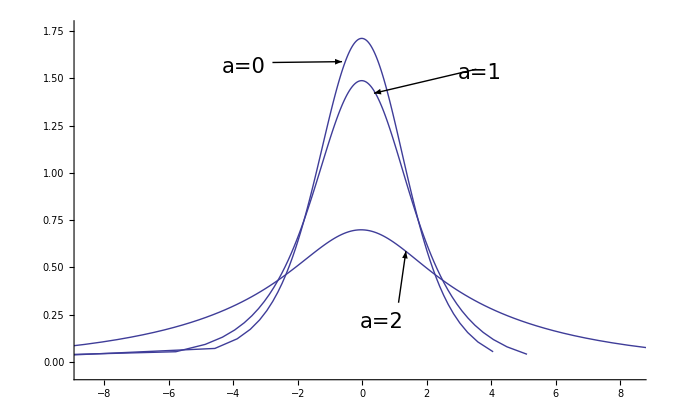

```mathematica
Plot[{F[x,2.1,1]-F[0,2.1,1],F[x,2.4,1]-F[0,2.4,1]},{x,0,2*Pi}]
```

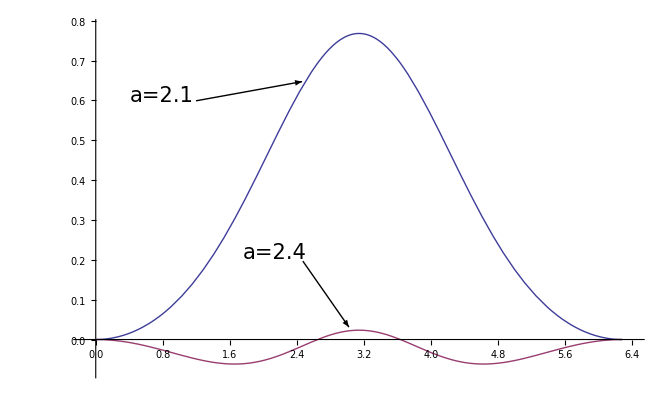

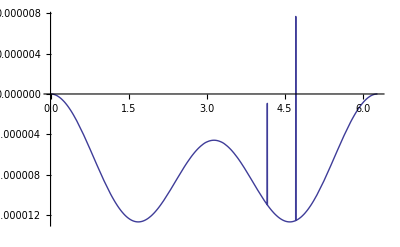

```mathematica
Plot[F[x,8.654,0.1]-F[0,8.654,0.1],{x,0,2*Pi}]
```

```mathematica
FindRoot[BesselJ[0,x],{x,11}]
```

{x→11.7915}

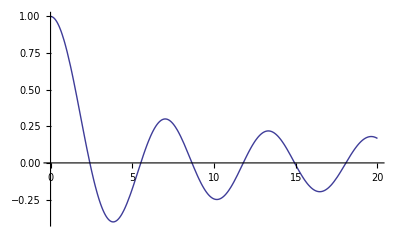

```mathematica
Plot[BesselJ[0,x],{x,0,20}]
```

```mathematica
IsHaveZero[a_,b_]:=Module[{},
Length[Select[Table[F[x,a,b]-F[0,a,b],{x,0,2*Pi,0.1}],#<0&]]>0
]
```

```mathematica
FindLessZero[b_,a0_,tol_]:=Module[{ab,k,i},
ab=a0;
For[k=1,k<tol,k++,
While[Not[IsHaveZero[ab,b]],ab+=10.0^(-k)];
ab-=10.0^(-k)
];
Return[ab];
];
FindMoreZero[b_,a0_,tol_]:=Module[{ab,k,i},
ab=a0;
For[k=1,k<tol,k++,
While[IsHaveZero[ab,b],ab+=10.0^(-k)];
ab-=10.0^(-k)
];
Return[ab];
];
```

```mathematica
ParallelTable[FindLessZero[b,0,4],{b,0.1,4.1,0.2}]//Timing
```

{1.669,{2.402,2.386,2.36,2.331,2.305,2.282,2.262,2.246,2.232,2.221,2.211}}

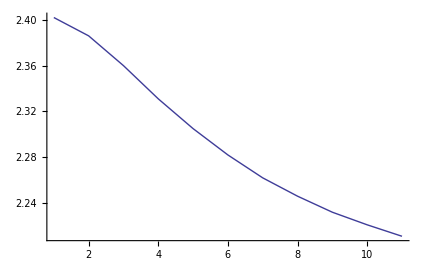

```mathematica
ListPlot[%[[2]],Joined->True]
```

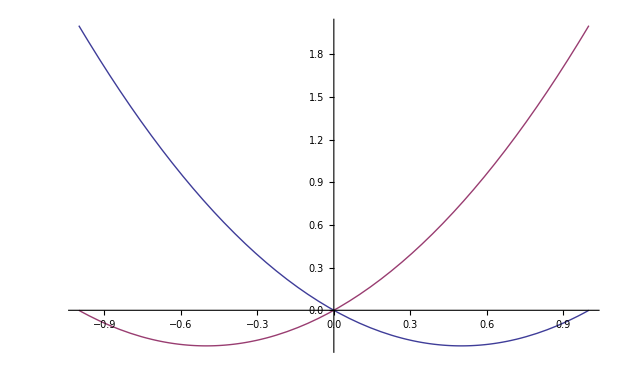

```mathematica
Plot[{p^2-p,p^2+p},{p,-1,1}]
```